```mathematica
Needs["VectorFieldPlots`"];
SetDirectory[NotebookDirectory[]];
p=ReadList["H.csv",Number,RecordLists-> True,RecordSeparators->{"\n","\r\n","\r",","}];
q=ReadList["H_fft.csv",Number,RecordLists-> True,RecordSeparators->{"\n","\r\n","\r",","}];
L=24;
Dimensions[p]
p=ArrayReshape[p,{46,15,L,L,3}];
q=ArrayReshape[q,{46,15,L,L}];
Dimensions[p]
```

{1192320,1}

{46,15,24,24,3}

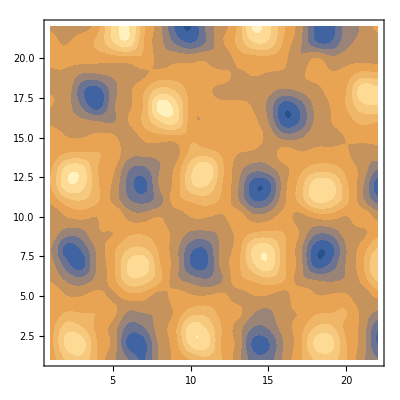

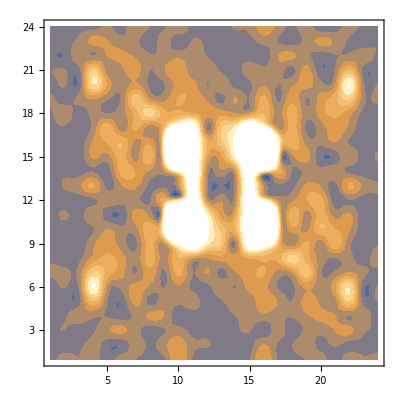

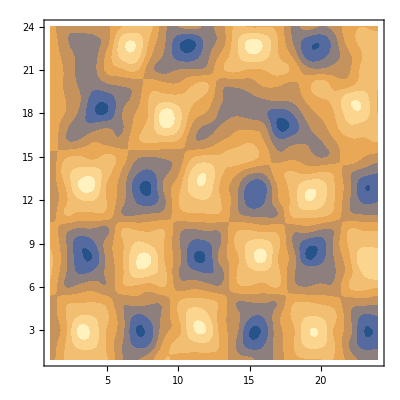

-Graphics3D-

```mathematica
p2=p[[14,1,All,All,All]];
fft=q[[14,1,All,All]];
edge=1;
chirality=Table[p2[[i,j]].(
     Cross[p2[[i+1,j]],p2[[i,j+1]]]
+Cross[p2[[i-1,j+1]],p2[[i-1,j]]]
+Cross[p2[[i,j+1]],p2[[i,j-1]]]
+Cross[p2[[i-1,j]],p2[[i-1,j-1]]]
+Cross[p2[[i,j-1]],p2[[i+1,j-1]]]
+Cross[p2[[i+1,j+1]],p2[[i,j+1]]]
+Cross[p2[[i-1,j+1]],p2[[i-1,j]]]
+Cross[p2[[i-1,j-1]],p2[[i,j-1]]]
+Cross[p2[[i+1,j-1]],p2[[i+1,j]]]),{i,1+edge,L-edge},{j,1+edge,L-edge}];
ListContourPlot[chirality,FrameTicksStyle->Directive[FontOpacity->0,FontSize->0], ContourStyle->None,InterpolationOrder->2]
ListContourPlot[fft,FrameTicksStyle->Directive[FontOpacity->0,FontSize->0], ContourStyle->None,InterpolationOrder->2]
ListContourPlot[p2[[All,All,3]],FrameTicksStyle->Directive[FontOpacity->0,FontSize->0], ContourStyle->None,InterpolationOrder->2]

coord =Flatten[Table[{x,y},{x,1,L,1},{y,1,L,1}],1];
CONFnewlist=Table[{{coord[[i]][[1]],coord[[i]][[2]],0},Flatten[p2,1][[i]]},{i,L*L}];
ListVectorFieldPlot3D[CONFnewlist,ScaleFactor->1,VectorHeads->True]
```